```mathematica
$Assumptions=vth∈Reals && vth > 0 && n >=0 && n∈Integers && kperp∈Reals &&kperp>=0 &&Oc∈Reals&& Oc>0 && omega∈Reals&&nu∈Reals&&nu>0&&kpar∈Reals&&kpar>=0wp∈Reals&&wp>0 && T∈Reals &&T>0 && alpha∈Reals && alpha>0;
```

```mathematica
valueSubsElc={vth->174105.3599459448,Oc->1758820.0107721633,nu->294.6517023103705,wp->17839863.659790836,T->1000}; 
valueSubsIon={vth->1019.464480807604,Oc->60.3033325979083,nu->0.7773786350631663,wp->104460.35291075318,T->1000}; 
valueSubsGen = {kperp->1.6377285093039773,kpar->9.28801992028526,Te->1000,alpha->15.364651294164071,nmax->0};
```

```mathematica
f0=Exp[-(vpar^2+vperp^2)/vth^2]/vth^3/Pi^(3/2);
```

```mathematica
dfdvpar = kpar*D[f0,vpar];
dfdvperp = n*D[f0,vperp]/(vperp/Oc);
```

```mathematica
UIntegrand = BesselJ[n,kperp*vperp/Oc]^2*f0/(omega-kpar*vpar-n*Oc-I*nu);
```

```mathematica
UIntegral = Integrate[Integrate[Integrate[UIntegrand,{vpar,-Infinity,Infinity}]*vperp,{vperp,0,Infinity}],{phi,0,2*Pi}];
```

```mathematica
U = I*nu*Sum[UIntegral,{n,-nmax,nmax}];
```

```mathematica
MIntegrand = BesselJ[n,kperp*vperp/Oc]^2*f0/((omega-kpar*vpar-n*Oc)^2+nu^2);
```

```mathematica
MIntegral = Integrate[Integrate[Integrate[MIntegrand,{vpar,-Infinity,Infinity}]*vperp,{vperp,0,Infinity}],{phi,0,2*Pi}];
```

```mathematica
M=nu/Abs[1+U]^2*(Sum[MIntegral,{n,-nmax,nmax}]-Abs[U]^2/nu^2);
```

```mathematica
chiIntegrand = BesselJ[n,kperp*vperp/Oc]^2*(dfdvpar+dfdvperp)/(omega-kpar*vpar-n*Oc-I*nu);
```

```mathematica
chiIntegral = Integrate[Integrate[Integrate[chiIntegrand,{vpar,-Infinity,Infinity}]*vperp,{vperp,0,Infinity}],{phi,0,2*Pi}];
```

```mathematica
chi = wp^2/(kpar^2+kperp^2)*Sum[chiIntegral,{n,-nmax,nmax}]/(1+U);
```

```mathematica
Ui = U /. valueSubsGen /.valueSubsIon;
Mi = M /. valueSubsGen /.valueSubsIon;
chii = chi /. valueSubsGen /.valueSubsIon;
Ue = U /. valueSubsGen /.valueSubsElc;
Me = M /. valueSubsGen /.valueSubsElc;
chie = chi /. valueSubsGen /.valueSubsElc;
```

```mathematica
epsilon = 1 + chie + chii;
```

```mathematica
S = 2*Abs[1-chie/epsilon]^2*Me+2*Abs[chie/epsilon]^2*Mi;
```

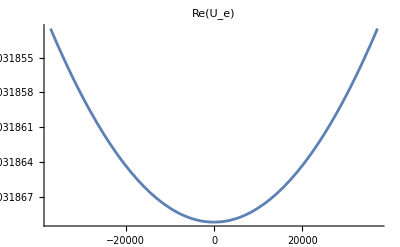

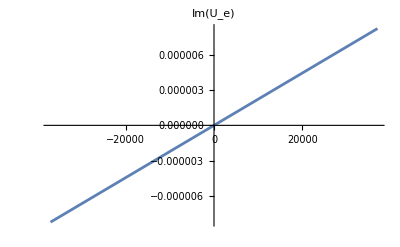

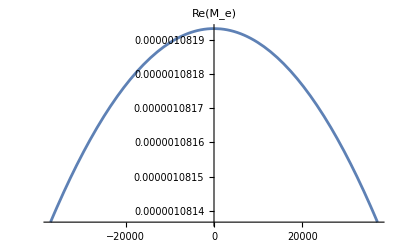

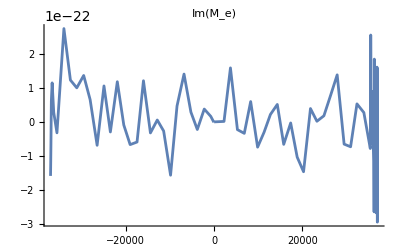

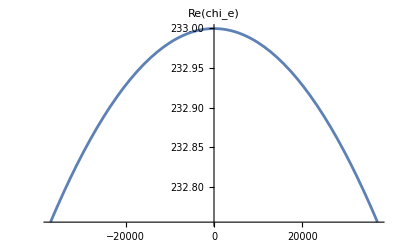

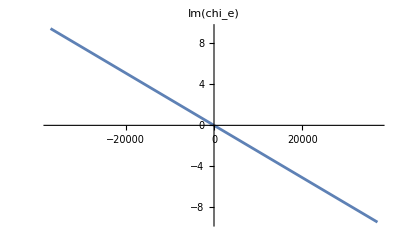

```mathematica
Plot[Re[Ue],{omega,-37000,37000},PlotRange->All,PlotLabel->"Re(U_e)"]
Plot[Im[Ue],{omega,-37000,37000},PlotRange->All,PlotLabel->"Im(U_e)"]
Plot[Re[Me],{omega,-37000,37000},PlotRange->All,PlotLabel->"Re(M_e)"]
Plot[Im[Me],{omega,-37000,37000},PlotRange->All,PlotLabel->"Im(M_e)"]
Plot[Re[chie],{omega,-37000,37000},PlotRange->All,PlotLabel->"Re(chi_e)"]
Plot[Im[chie],{omega,-37000,37000},PlotRange->All,PlotLabel->"Im(chi_e)"]
```

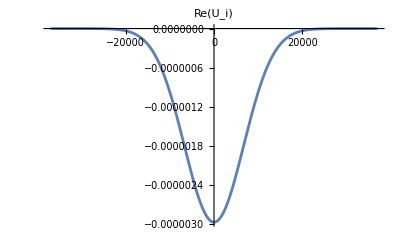

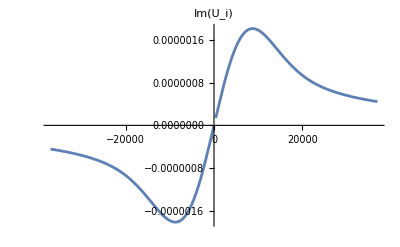

General::munfl: Exp[-797.094] is too small to represent as a normalized machine number; precision may be lost.

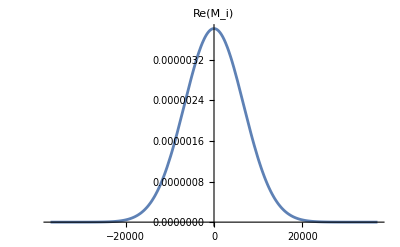

General::munfl: Exp[-797.094] is too small to represent as a normalized machine number; precision may be lost.

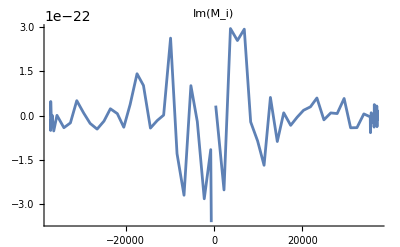

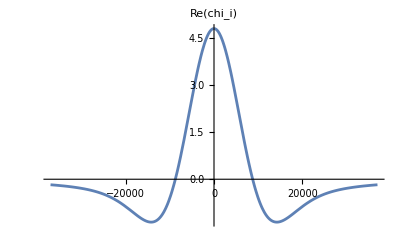

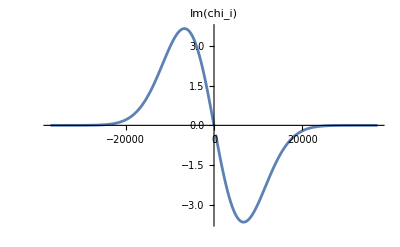

```mathematica
Plot[Re[Ui],{omega,-37000,37000},PlotRange->All,PlotLabel->"Re(U_i)"]
Plot[Im[Ui],{omega,-37000,37000},PlotRange->All,PlotLabel->"Im(U_i)"]
Plot[Re[Mi],{omega,-37000,37000},PlotRange->All,PlotLabel->"Re(M_i)"]
Plot[Im[Mi],{omega,-37000,37000},PlotRange->All,PlotLabel->"Im(M_i)"]
Plot[Re[chii],{omega,-37000,37000},PlotRange->All,PlotLabel->"Re(chi_i)"]
Plot[Im[chii],{omega,-37000,37000},PlotRange->All,PlotLabel->"Im(chi_i)"]
```

General::munfl: Exp[-797.094] is too small to represent as a normalized machine number; precision may be lost.

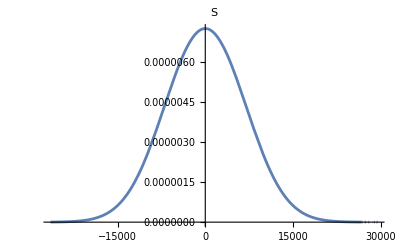

```mathematica
Plot[S,{omega,-37000,37000},PlotRange->All,PlotLabel->"S"]
```

```mathematica
FullSimplify[chiIntegral]
```

1/(kpar √π vth^3)2 ⅇ^(-(kperp^2 vth^2)/(2 Oc^2)) BesselI[n,(kperp^2 vth^2)/(2 Oc^2)] (kpar √π vth+ⅇ^((nu-ⅈ n Oc+ⅈ omega)^2/(kpar^2 vth^2)) (nu+ⅈ omega) (π Erf[(nu-ⅈ n Oc+ⅈ omega)/(kpar vth)]-ⅈ (Log[kpar/(ⅈ nu+n Oc-omega)]-Log[kpar/(-ⅈ nu-n Oc+omega)])))

```mathematica
(* Show what U would be looking like *)
FullSimplify[I*nu*UIntegral]
```

-1/(kpar √π vth)ⅈ ⅇ^((nu-ⅈ n Oc+ⅈ omega)^2/(kpar^2 vth^2)-(kperp^2 vth^2)/(2 Oc^2)) nu BesselI[n,(kperp^2 vth^2)/(2 Oc^2)] (π Erfi[(ⅈ nu+n Oc-omega)/(kpar vth)]+Log[kpar/(ⅈ nu+n Oc-omega)]-Log[kpar/(-ⅈ nu-n Oc+omega)])

```mathematica
(*Show what M looks like*)
FullSimplify[nu*MIntegral]
```

1/(2 kpar √π vth)ⅈ ⅇ^((nu^2-(-n Oc+omega)^2-2 ⅈ nu (n Oc+omega))/(kpar^2 vth^2)-(kperp^2 vth^2)/(2 Oc^2)) BesselI[n,(kperp^2 vth^2)/(2 Oc^2)] (ⅇ^((4 ⅈ nu omega)/(kpar^2 vth^2)) (π Erfi[(ⅈ nu+n Oc-omega)/(kpar vth)]+Log[kpar/(ⅈ nu+n Oc-omega)]-Log[kpar/(-ⅈ nu-n Oc+omega)])+ⅇ^((4 ⅈ n nu Oc)/(kpar^2 vth^2)) (π Erfi[(ⅈ nu-n Oc+omega)/(kpar vth)]-Log[kpar/(-ⅈ nu+n Oc-omega)]+Log[kpar/(ⅈ nu-n Oc+omega)]))

```mathematica
FullSimplify[wp^2*chiIntegral/(kpar^2+kperp^2)]
```

(2 ⅇ^(-(kperp^2 vth^2)/(2 Oc^2)) wp^2 BesselI[n,(kperp^2 vth^2)/(2 Oc^2)] (kpar √π vth+ⅇ^((nu-ⅈ n Oc+ⅈ omega)^2/(kpar^2 vth^2)) (nu+ⅈ omega) (π Erf[(nu-ⅈ n Oc+ⅈ omega)/(kpar vth)]-ⅈ (Log[kpar/(ⅈ nu+n Oc-omega)]-Log[kpar/(-ⅈ nu-n Oc+omega)]))))/(kpar (kpar^2+kperp^2) √π vth^3)

```mathematica
Integrate[vperp*BesselJ[n,kperp*vperp/Oci]^2*Exp[-vperp^2/vth^2],{vperp,0,Infinity}]
```

1/2 ⅇ^(-(kperp^2 vth^2)/(2 Oci^2)) vth^2 BesselI[n,(kperp^2 vth^2)/(2 Oci^2)]

```mathematica
Integrate[BesselJ[n,kperp*vperp/Oci]*(BesselJ[n-1,kperp*vperp/Oci]-BesselJ[n+1,kperp*vperp/Oci])*Exp[-vperp^2/vth^2],{vperp,0,Infinity}]
```

ConditionalExpression[1/kperp 2^(-1-2 n) (1/Oci^2)^(1/2+n) (kperp vth)^(2 n) Gamma[2 n] (2 Oci^2 HypergeometricPFQRegularized[{n,1/2+n},{2 n,1+n},-(kperp^2 vth^2)/Oci^2]-kperp^2 n (1+2 n) vth^2 HypergeometricPFQRegularized[{1+n,3/2+n},{2+n,2+2 n},-(kperp^2 vth^2)/Oci^2]), n>0]